```mathematica
Δqed=ω (*α/(45 π)(B/Subscript[B, c])^2*)ζ;
Δpl=-ωp^2/(2 ω);
```

```mathematica
M={{ω+Δxx,Δxy,g Bx /2},{Δyx,ω + Δyy,g By /2},{g Bx/2, g By/2, ω-m^2/(2ω)}}/.{Δxy-> 0,Δyx-> 0,Bx-> 0,By-> B,Δxx-> Δqed+Δpl,Δyy-> Δqed+Δpl}(*//MatrixForm*)
```

{{ω+ζ ω-ωp^2/(2 ω),0,0},{0,ω+ζ ω-ωp^2/(2 ω),(B g)/2},{0,(B g)/2,-m^2/(2 ω)+ω}}

```mathematica
ksol=Solve[Det[M-k IdentityMatrix[3]]==0,k]//Simplify
```

{{k→ω+ζ ω-ωp^2/(2 ω)},{k→-(m^2 ω-4 ω^3-2 ζ ω^3+ω ωp^2+√(ω^2 (m^4+4 B^2 g^2 ω^2+m^2 (4 ζ ω^2-2 ωp^2)+(-2 ζ ω^2+ωp^2)^2)))/(4 ω^2)},{k→(-m^2 ω+4 ω^3+2 ζ ω^3-ω ωp^2+√(ω^2 (m^4+4 B^2 g^2 ω^2+m^2 (4 ζ ω^2-2 ωp^2)+(-2 ζ ω^2+ωp^2)^2)))/(4 ω^2)}}

```mathematica
PaniRes0=D[k/.ksol⟦1⟧,ω]//Simplify
```

1+ζ+ωp^2/(2 ω^2)

```mathematica
Normal[Series[D[k/.ksol⟦3⟧,ω]/.ωp->ω Sqrt[X],{ζ,0,1},{X,0,1}]]//Simplify
```

1/4 (4+m^2/ω^2-m^4/(ω √(ω^2 (m^4+4 B^2 g^2 ω^2)))+X (1-(m^6 ω^3)/((ω^2 (m^4+4 B^2 g^2 ω^2))^(3/2))+(2 m^2 ω)/(√(ω^2 (m^4+4 B^2 g^2 ω^2))))+1/((m^4+4 B^2 g^2 ω^2)^3)2 ζ (m^4 (m^4+4 B^2 g^2 ω^2)^2+4 B^2 g^2 ω^2 (m^4+4 B^2 g^2 ω^2)^2-12 B^2 g^2 m^4 X ω^3 √(ω^2 (m^4+4 B^2 g^2 ω^2))+(m^6 (ω^2 (m^4+4 B^2 g^2 ω^2))^(3/2))/ω^3))

```mathematica
MyRes1=1/4 (4+m^2/ω^2+m^4/(ω √(ω^2 (m^4+4 B^2 g^2 ω^2)))+X (1+(m^6 ω^3)/((ω^2 (m^4+4 B^2 g^2 ω^2))^(3/2))-(2 m^2 ω)/(√(ω^2 (m^4+4 B^2 g^2 ω^2))))+1/((m^4+4 B^2 g^2 ω^2)^3)2 ζ (m^4 (m^4+4 B^2 g^2 ω^2)^2+4 B^2 g^2 ω^2 (m^4+4 B^2 g^2 ω^2)^2-(m^6 (ω^2 (m^4+4 B^2 g^2 ω^2))^(3/2))/ω^3))/.X-> ωp^2/ω^2//Simplify;
MyRes2=1/4 (4+m^2/ω^2-m^4/(ω √(ω^2 (m^4+4 B^2 g^2 ω^2)))+X (1-(m^6 ω^3)/((ω^2 (m^4+4 B^2 g^2 ω^2))^(3/2))+(2 m^2 ω)/(√(ω^2 (m^4+4 B^2 g^2 ω^2))))+1/((m^4+4 B^2 g^2 ω^2)^3)2 ζ (m^4 (m^4+4 B^2 g^2 ω^2)^2+4 B^2 g^2 ω^2 (m^4+4 B^2 g^2 ω^2)^2+(m^6 (ω^2 (m^4+4 B^2 g^2 ω^2))^(3/2))/ω^3))/.X-> ωp^2/ω^2//Simplify;
```

```mathematica
Clear[Y]
Y=1/Sqrt[1+η^2];
(*η=2 g B ω/m^2; *)
PaniRes1=1+ζ/2+(m^2+ωp^2)/(4 ω^2)+1/2(Y^3 ζ+(ωp^2)/(2 ω^2)(2 Y -Y^3)-m^2 Y/(2 ω^2));
PaniRes2=1+ζ/2+(m^2+ωp^2)/(4 ω^2)-1/2(Y^3 ζ+(ωp^2)/(2 ω^2)(2 Y -Y^3)-m^2 Y/(2 ω^2));
```

```mathematica
(*Simplify[MyRes1-PaniRes2,Assumptions->{m>0,ω>0,ωp>0,g>0,B>0}]*)
```

cicclotrone frequency:

```mathematica
e B/(m (*c*))/.B-> 10^-3 10^-4 kg/(Coul /s s^2)/.m-> 9.10938356×10^-13 kg /. e-> 1.60217662×10^-19 Coul /. c-> 2.99792458 10^8 met /s
```

(1.75882×10^-14)/s

### No vacuum polarization (ζ=0)

#### Y∼1

```mathematica
Normal[Series[PaniRes0,{ζ,0,0}]]
```

1+ωp^2/(2 ω^2)

typo in (38)? why is m^2 Y /omega^2 neglected? As a consequence, also (41) is to be corrected

```mathematica
Normal[Series[PaniRes1/.ζ-> 0,{η,0,4}]](*//Simplify*)
```

1+ωp^2/(2 ω^2)+(η^2 (m^2+ωp^2))/(8 ω^2)-(3 η^4 (m^2+3 ωp^2))/(32 ω^2)

```mathematica
Normal[Series[PaniRes2/.ζ-> 0,{η,0,4}]]
```

1+m^2/(2 ω^2)+(η^2 (-m^2-ωp^2))/(8 ω^2)+(3 η^4 (m^2+3 ωp^2))/(32 ω^2)

```mathematica
-+
```

```mathematica
Subscript[ΔT, axion,1]=Integrate[(3 η^4 (m^2+3 ωp^2))/(32 ω^2)/.η-> 2 g B ω/m^2/.ω-> 2π ν,{x,0,d}]
```

(6 B^4 d g^4 π^2 ν^2 (m^2+3 ωp^2))/m^8

#### Y∼0

```mathematica
Normal[Series[PaniRes0,{ζ,0,0}]]
```

1+ωp^2/(2 ω^2)

```mathematica
Normal[Series[PaniRes1/.ζ-> 0/.η-> 1/X,{X,0,0}]]/.X-> 1/η(*//Simplify*)
```

1+m^2/(4 ω^2)-m^2/(4 √(η^2) ω^2)+ωp^2/(4 ω^2)+ωp^2/(2 √(η^2) ω^2)

```mathematica
Normal[Series[PaniRes2/.ζ-> 0/.η-> 1/X,{X,0,0}]]/.X-> 1/η(*//Simplify*)
```

1+m^2/(4 ω^2)+m^2/(4 √(η^2) ω^2)+ωp^2/(4 ω^2)-ωp^2/(2 √(η^2) ω^2)

+-

```mathematica
Simplify[m^2/(4 √(η^2) ω^2)-ωp^2/(2 √(η^2) ω^2)/.ω-> 2π ν,Assumptions->{η>0}]
```

(m^2-2 ωp^2)/(16 π^2 η ν^2)

```mathematica
Subscript[ΔT, axion,2]=Integrate[(m^2-2 ωp^2)/(16 π^2 η ν^2)/.η-> 2 g B ω/m^2/.ω-> 2π ν,{x,0,d}]
```

(d m^2 (m^2-2 ωp^2))/(64 B g π^3 ν^3)

### Predictions

```mathematica
Block[{ne=0.01,d=10^3,ν=1 10^9 s^-1},
K=4.149 10^-3;
DM=d ne;
{K DM/ν^2 s,DM}]
```

{4.149×10^-20 s^3,10.}

```mathematica
Block[{ν=1 10^9 s^-1},K DM/((ν/10^9 s)^2)s]
```

0.04149 s

OK!

We focus on the second contribution.

```mathematica
Subscript[ΔT, axion,2]/.ωp-> Sqrt[e^2 ne / (me ϵ0 )]
```

```mathematica
Block[{d=1 10^3 (3.0857 10^16 met), B= 10^-3 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,m= 10^-11 (1.602 10^-19 (kg met^2)/s^2), me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=0.01 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ν=1 10^9 s^-1},

Simplify[{(*(d m^2 (m^2-(2 e^2 ne)/(me ϵ0)))/(64 B g π^3 ν^3),*)(d m^2(m^2 Sqrt[1/ℏ^4]))/(64 B g π^3 ν^3)Sqrt[1/(c^7 ϵ0 ℏ^5)],Sqrt[1/(c^7 ϵ0 ℏ^5)](d m^2 (-(2 e^2 ne)/(me ϵ0)))/(64 B g π^3 ν^3)},Assumptions->{met>0,s>0,Coul>0,kg>0}]
]
```

{9.37522×10^6 s,-2.58755×10^6 s}

```mathematica
s^20/(kg^10 met^29)(kg met^2/s)^10(met/s)^9
```

s

```mathematica
Block[{d=1 10^3 (3.0857 10^16 met), B= 10^-3 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,m= 1.6 10^-15 (1.602 10^-19 (kg met^2)/s^2), me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=0.01 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ν=1 10^9 s^-1},

Simplify[{(6 B^4 d g^4 π^2 ν^2 ((*m^2+*)3 Sqrt[e^2 ne / (me ϵ0 )]^2))/m^8 ϵ0^2 (ℏ c)^10/c,Sqrt[1/(c^7 ϵ0 ℏ^5)](d m^2 (-(2 e^2 ne)/(me ϵ0)))/(64 B g π^3 ν^3)},Assumptions->{met>0,s>0,Coul>0,kg>0}]
]
```

{0.00363544 s,-0.0662412 s}

sort of ok!

#### Plots

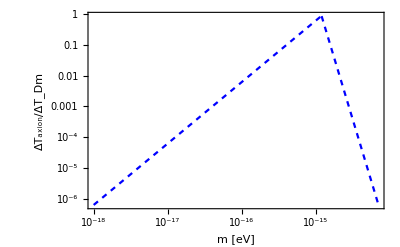

```mathematica
Block[{d=1 10^3 (3.0857 10^16 met), B= 10^-3 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,(*m= 10^-15 (1.602 10^-19 (kg met^2)/s^2),*) me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=0.01 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ν=1 10^9 s^-1},
plotblue=Show[{LogLogPlot[Simplify[Abs[((d (m(1.602 10^-19 (kg met^2)/s^2))^2((m(1.602 10^-19 (kg met^2)/s^2))^2 Sqrt[1/ℏ^4]))/(64 B g π^3 ν^3)Sqrt[1/(c^7 ϵ0 ℏ^5)]+Sqrt[1/(c^7 ϵ0 ℏ^5)](d (m (1.602 10^-19 (kg met^2)/s^2))^2 (-(2 e^2 ne)/(me ϵ0)))/(64 B g π^3 ν^3))/(K DM/((ν/10^9 s)^2)s)],Assumptions->{met>0,s>0,Coul>0,kg>0}],{m,10^-18 ,1.15 10^-15 },PlotRange->{{10^-18,7 10^-15},All},PlotStyle->{Blue,Dashing[0.01]},Frame->True,FrameLabel->{"m [eV]","ΔT_axion/ΔT_Dm"}],LogLogPlot[Simplify[Abs[((6 B^4 d g^4 π^2 ν^2 ((*m^2+*)3 Sqrt[e^2 ne / (me ϵ0 )]^2))/((m(1.602 10^-19 (kg met^2)/s^2))^8)ϵ0^2 (ℏ c)^10/c)/(K DM/((ν/10^9 s)^2)s)],Assumptions->{met>0,s>0,Coul>0,kg>0}],{m,1.2 10^-15,7 10^-15},PlotRange->All,PlotStyle->{Blue,Dashing[0.01]}]}(*,PlotRange->{{10^-18,1.9 10^-15},{10^-6,1.2}}*)]
]
```

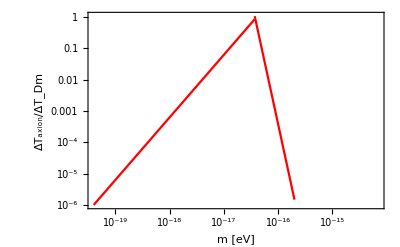

```mathematica
Block[{d=1 10^3 (3.0857 10^16 met), B= 10^-6 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,(*m= 10^-15 (1.602 10^-19 (kg met^2)/s^2),*) me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=0.01 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ν=1 10^9 s^-1},
plotred=Show[{LogLogPlot[Simplify[Abs[((d (m(1.602 10^-19 (kg met^2)/s^2))^2((m(1.602 10^-19 (kg met^2)/s^2))^2 Sqrt[1/ℏ^4]))/(64 B g π^3 ν^3)Sqrt[1/(c^7 ϵ0 ℏ^5)]+Sqrt[1/(c^7 ϵ0 ℏ^5)](d (m (1.602 10^-19 (kg met^2)/s^2))^2 (-(2 e^2 ne)/(me ϵ0)))/(64 B g π^3 ν^3))/(K DM/((ν/10^9 s)^2)s)],Assumptions->{met>0,s>0,Coul>0,kg>0}],{m,4 10^-20,3.7 10^-17 },PlotRange->{{4 10^-20,7 10^-15},All},PlotStyle->{Red},Frame->True,FrameLabel->{"m [eV]","ΔT_axion/ΔT_Dm"}],LogLogPlot[Simplify[Abs[((6 B^4 d g^4 π^2 ν^2 ((*m^2+*)3 Sqrt[e^2 ne / (me ϵ0 )]^2))/((m(1.602 10^-19 (kg met^2)/s^2))^8)ϵ0^2 (ℏ c)^10/c)/(K DM/((ν/10^9 s)^2)s)],Assumptions->{met>0,s>0,Coul>0,kg>0}],{m,3.7 10^-17,2 10^-16},PlotRange->All,PlotStyle->{Red}]}(*,PlotRange->{{10^-18,1.9 10^-15},{10^-6,1.2}}*)]
]
```

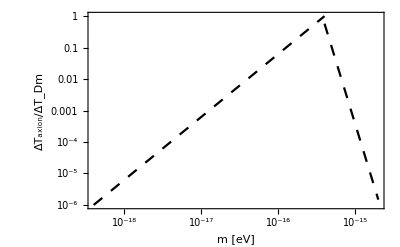

```mathematica
Block[{d=1 10^3 (3.0857 10^16 met), B= 10^-3 10^-4 kg/(Coul  s), g=10^-11  (10^9 1.602 10^-19 (kg met^2)/s^2)^-1,(*m= 10^-15 (1.602 10^-19 (kg met^2)/s^2),*) me= 9.10938356 10^-31 kg(*, α=1/137*)(*, Gauss=10^-4 kg/(Coul /s s^2)*),ne=0.01 (10^-2 met)^-3,ϵ0=8.854 10^-12 met^-1 s^2 Coul^2/(met^2 kg), e=1.602 10^-19 Coul,c=2.99 10^8 met/s,ℏ=1.055 10^-34 kg met^2/s,ν=0.1 10^9 s^-1},
plotblack=Show[{LogLogPlot[Simplify[Abs[((d (m(1.602 10^-19 (kg met^2)/s^2))^2((m(1.602 10^-19 (kg met^2)/s^2))^2 Sqrt[1/ℏ^4]))/(64 B g π^3 ν^3)Sqrt[1/(c^7 ϵ0 ℏ^5)]+Sqrt[1/(c^7 ϵ0 ℏ^5)](d (m (1.602 10^-19 (kg met^2)/s^2))^2 (-(2 e^2 ne)/(me ϵ0)))/(64 B g π^3 ν^3))/(K DM/((ν/10^9 s)^2)s)],Assumptions->{met>0,s>0,Coul>0,kg>0}],{m,4 10^-19,4 10^-16 },PlotRange->{{4 10^-19,2 10^-15},All},PlotStyle->{Black,Dashing[0.02]},Frame->True,FrameLabel->{"m [eV]","ΔT_axion/ΔT_Dm"}],LogLogPlot[Simplify[Abs[((6 B^4 d g^4 π^2 ν^2 ((*m^2+*)3 Sqrt[e^2 ne / (me ϵ0 )]^2))/((m(1.602 10^-19 (kg met^2)/s^2))^8)ϵ0^2 (ℏ c)^10/c)/(K DM/((ν/10^9 s)^2)s)],Assumptions->{met>0,s>0,Coul>0,kg>0}],{m,4 10^-16,2 10^-15},PlotRange->All,PlotStyle->{Black,Dashing[0.02]},Frame->True,FrameLabel->{"m [eV]","ΔT_axion/ΔT_Dm"}]}(*,PlotRange->{{10^-18,1.9 10^-15},{10^-6,1.2}}*)]
]
```

#### Plots together

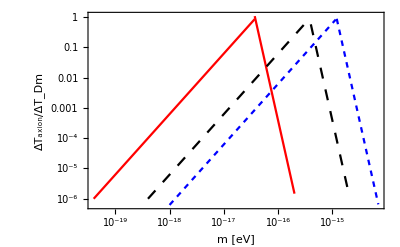

```mathematica
Show[{plotred,plotblack,plotblue}]
```

(I don' t agree with the order of magnitude, but I agree with discarding the mass term.) Moreover, this can take both signs (the two solutions for the velocity)